quad diagram

{2,1,5,5,1,1,1,0.01,0.01}

{{0,0},{0,1},{1,0},{0,10},{10,10},{5,5},{4,11/2},{6,11/2}}

{{0,10},{10,10},{5,5}}

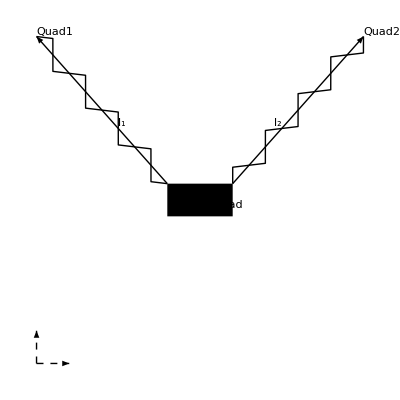

```mathematica
(*geometric properties:*)
{Subscript[l, p]=2, (* length of payload box *)
Subscript[h, p]=1, (* hight of payload box *)
Subscript[l, 1]=√25,
Subscript[l, 2]=√25,
Subscript[m, 1]=1,Subscript[m, 2]=1,Subscript[m, p]=1,
Subscript[k, 1]=1/100.,
Subscript[k, 2]=1./100
}
(*locations:*)
{Iorigin={0,0},
IaxisX = {0,1},
IaxisZ = {1,0},
Quad1CenterPos = {Subscript[x, i],Subscript[z, i]} /. i->1,
Quad2CenterPos = {Subscript[x, i],Subscript[z, i]} /. i->2,
PayloadCenterPos = {Subscript[x, i],Subscript[z, i]} /. i->p,
HangPoint1=PayloadCenterPos-{Subscript[l, p]/2,-Subscript[h, p]/2},
HangPoint2=PayloadCenterPos+{Subscript[l, p]/2,Subscript[h, p]/2}}
(*initial locations:*)
scale0 = 10;
{{Subscript[x, 1]=0,Subscript[z, 1]=scale0},{Subscript[x, 2]=scale0,Subscript[z, 2]=scale0},{Subscript[x, p]=scale0/2,Subscript[z, p]=scale0/2}}

(*labels*)
PayloadLabel =Text["Payload",{Subscript[x, i],Subscript[z, i]} /. i->p,{-1,2.5(+1+Subscript[h, p]/2)}];
Quad1Label =Text["Quad1",{Subscript[x, i],Subscript[z, i]} /. i->1,{-1,-1}];
Quad2Label =Text["Quad2",{Subscript[x, i],Subscript[z, i]} /. i->2,{-1,-1}];
l1Label=Text["l_1",{(Subscript[x, 1]+Subscript[x, p])/2,(Subscript[z, 1]+Subscript[z, p])/2},{-2,1}];
l2Label=Text["l_2",{(Subscript[x, 2]+Subscript[x, p])/2,(Subscript[z, 2]+Subscript[z, p])/2},{2,1}];
(*general additions *)
spring[r_: {1,0},n_: 20,w_: 1,origin_:{0,0}]:=Line@Transpose[{r-origin,-Cross[r-origin]}.{(#-1)/(2 n),Re[I^#] w/Norm[r-origin]}+origin]&@Range[2 n+1];
(*elements:*)
Iarrows={Dashed,Arrowheads[Small],Arrow[{Iorigin,IaxisX}],Arrow[{Iorigin,IaxisZ}]};
Labels = {PayloadLabel,Quad1Label,Quad2Label,l1Label,l2Label};
Cabels ={Arrowheads[{-Small,Small}],Arrow[{HangPoint1,Quad1Pos}],Arrow[{HangPoint2,Quad2Pos}]};
(*spr1=spring[r/.r->HangPoint1+{-1,1},n/.n->8,w/.w->1/3.,origin/.origin->Quad1Pos+{-1,-1}];*)
spr1=spring[r/.r->HangPoint1,n/.n->8,1/3.,origin/.origin->Quad1Pos];
spr2=spring[HangPoint2,8,1/3,Quad2Pos];
PayloadBox={Rectangle[HangPoint1-{0,Subscript[h, p]},HangPoint2]};
a=Graphics[{Iarrows,Labels,Cabels,spr1,spr2,PayloadBox}]
```